## Berry curvature

### formulae

```mathematica
Clear[ham,k,v1,v2,ψ1,ψ2,kx,ky,kz];(* -Graphics-*)
ass=Assumptions->{k,θ,ϕ,kx,ky,kz,k0,kp,κp}∈ Reals &&  k>0 && k0>0 && kp>0;
rep={kx-> kp Cos[ϕ],ky-> kp Sin[ϕ],kz-> k Cos[θ]};
sx=PauliMatrix[1];sy=PauliMatrix[2]; sz=PauliMatrix[3];s0=IdentityMatrix[2];

ham= -kx kz sx-ky kz sy+(((kx^2+ky^2-kz^2)-k0^2)/2)sz//FullSimplify;
ham//MatrixForm
{en,evec}=FullSimplify[Eigensystem[ham],ass]/.kx^2->kp^2-ky^2;
en
evec
```

(1/2 (-k0^2+kx^2+ky^2-kz^2) | -((kx-ⅈ ky) kz)
-((kx+ⅈ ky) kz) | 1/2 (k0^2-kx^2-ky^2+kz^2))

{-1/2 √(k0^4-2 k0^2 (kp^2-kz^2)+(kp^2+kz^2)^2),1/2 √(k0^4-2 k0^2 (kp^2-kz^2)+(kp^2+kz^2)^2)}

{{(k0^2-kp^2+kz^2+√((-k0^2+kp^2)^2+2 (k0^2+kp^2) kz^2+kz^4))/(2 (kx+ⅈ ky) kz),1},{-(-k0^2+kp^2-kz^2+√((-k0^2+kp^2)^2+2 (k0^2+kp^2) kz^2+kz^4))/(2 (kx+ⅈ ky) kz),1}}

```mathematica
ent=(-k0^2+kp^2)^2+(2 k0^2-kp^2) kz^2+kz^4/.{kz->δ kz,kp->k0+δ κp};
Normal[Series[ent,{δ,0,2}]//FullSimplify]/.δ->1
```

k0^2 (kz^2+4 κp^2)

```mathematica
(* -Graphics- *)
```

```mathematica
derx=D[ham,kx];dery=D[ham,ky];derz=D[ham,kz]/.kx^2->kp^2-ky^2;
vec=evec;
vecdag=FullSimplify[Conjugate[vec], ass]
```

{{(k0^2-kp^2+kz^2+√((k0^2-kp^2)^2+2 (k0^2+kp^2) kz^2+kz^4))/(2 (kx-ⅈ ky) kz),1},{(k0^2-kp^2+kz^2-√((k0^2-kp^2)^2+2 (k0^2+kp^2) kz^2+kz^4))/(2 (kx-ⅈ ky) kz),1}}

```mathematica
Clear[omx, omy, omz];omx[i_]:=-ⅈ∑_(j=1)^2 If[j≠i,( (vecdag[[i]].(dery.vec[[j]]))*(vecdag[[j]].(derz.vec[[i]]))-(vecdag[[i]].(derz.vec[[j]]))*(vecdag[[j]].(dery.vec[[i]])))/((vecdag[[i]].vec[[i]])*(vecdag[[j]].vec[[j]])*(en[[i]]-en[[j]])^2),0]/.kx^2->kp^2-ky^2


omy[i_]:=-ⅈ∑_(j=1)^2 If[j≠i,( (vecdag[[i]].(derz.vec[[j]]))*(vecdag[[j]].(derx.vec[[i]]))-(vecdag[[i]].(derx.vec[[j]]))*(vecdag[[j]].(derz.vec[[i]])))/((vecdag[[i]].vec[[i]])*(vecdag[[j]].vec[[j]])*(en[[i]]-en[[j]])^2),0]/.kx^2->kp^2-ky^2


omz[i_]:=-ⅈ∑_(j=1)^2 If[j≠i,( (vecdag[[i]].(derx.vec[[j]]))*(vecdag[[j]].(dery.vec[[i]]))-(vecdag[[i]].(dery.vec[[j]]))*(vecdag[[j]].(derx.vec[[i]])))/((vecdag[[i]].vec[[i]])*(vecdag[[j]].vec[[j]])*(en[[i]]-en[[j]])^2),0]/.kx^2->kp^2-ky^2
val=1;
FullSimplify[{omx[val],omy[val],omz[val]}, ass]/.{kx^2->kp^2-ky^2,(kx^2+ky^2)->kp^2}
FullSimplify[%/.rep,ass]
Print["band 2"];
val=2;
FullSimplify[{omx[val],omy[val],omz[val]}, ass]/.{kx^2->kp^2-ky^2,(kx^2+ky^2)->kp^2}
FullSimplify[%/.rep,ass]
```

{(-2 (k0-kp) kp^2 (k0+kp) kx kz+2 kp^2 kx kz^3)/(√((k0^2-kp^2)^2+(2 k0^2-kp^2) kz^2+kz^4) (4 kp^2 (k0^2-kp^2)^2+(-5 kp^4+kp^2 (8 k0^2+kp^2)) kz^2+4 kp^2 kz^4)),(-2 (k0-kp) kp^2 (k0+kp) ky kz+2 kp^2 ky kz^3)/(√((k0^2-kp^2)^2+(2 k0^2-kp^2) kz^2+kz^4) (4 kp^2 (k0^2-kp^2)^2+(-5 kp^4+kp^2 (8 k0^2+kp^2)) kz^2+4 kp^2 kz^4)),(2 kp^2 kz^2 (k0^2+kp^2+kz^2))/(√((k0^2-kp^2)^2+(2 k0^2-kp^2) kz^2+kz^4) (4 kp^2 (k0^2-kp^2)^2+(-5 kp^4+kp^2 (8 k0^2+kp^2)) kz^2+4 kp^2 kz^4))}

{(k kp Cos[θ] (k^2-2 k0^2+2 kp^2+k^2 Cos[2 θ]) Cos[ϕ])/(4 ((k0^2-kp^2)^2+k^2 (2 k0^2-kp^2) Cos[θ]^2+k^4 Cos[θ]^4)^(3/2)),(k kp Cos[θ] (k^2-2 k0^2+2 kp^2+k^2 Cos[2 θ]) Sin[ϕ])/(4 ((k0^2-kp^2)^2+k^2 (2 k0^2-kp^2) Cos[θ]^2+k^4 Cos[θ]^4)^(3/2)),(k^2 Cos[θ]^2 (k0^2+kp^2+k^2 Cos[θ]^2))/(2 ((k0^2-kp^2)^2+k^2 (2 k0^2-kp^2) Cos[θ]^2+k^4 Cos[θ]^4)^(3/2))}

band 2

{(2 (k0-kp) kp^2 (k0+kp) kx kz-2 kp^2 kx kz^3)/(√((k0^2-kp^2)^2+(2 k0^2-kp^2) kz^2+kz^4) (4 kp^2 (k0^2-kp^2)^2+(-5 kp^4+kp^2 (8 k0^2+kp^2)) kz^2+4 kp^2 kz^4)),(2 (k0-kp) kp^2 (k0+kp) ky kz-2 kp^2 ky kz^3)/(√((k0^2-kp^2)^2+(2 k0^2-kp^2) kz^2+kz^4) (4 kp^2 (k0^2-kp^2)^2+(-5 kp^4+kp^2 (8 k0^2+kp^2)) kz^2+4 kp^2 kz^4)),-(2 kp^2 kz^2 (k0^2+kp^2+kz^2))/(√((k0^2-kp^2)^2+(2 k0^2-kp^2) kz^2+kz^4) (4 kp^2 (k0^2-kp^2)^2+(-5 kp^4+kp^2 (8 k0^2+kp^2)) kz^2+4 kp^2 kz^4))}

{-(k kp Cos[θ] (k^2-2 k0^2+2 kp^2+k^2 Cos[2 θ]) Cos[ϕ])/(4 ((k0^2-kp^2)^2+k^2 (2 k0^2-kp^2) Cos[θ]^2+k^4 Cos[θ]^4)^(3/2)),-(k kp Cos[θ] (k^2-2 k0^2+2 kp^2+k^2 Cos[2 θ]) Sin[ϕ])/(4 ((k0^2-kp^2)^2+k^2 (2 k0^2-kp^2) Cos[θ]^2+k^4 Cos[θ]^4)^(3/2)),-(k^2 Cos[θ]^2 (k0^2+kp^2+k^2 Cos[θ]^2))/(2 ((k0^2-kp^2)^2+k^2 (2 k0^2-kp^2) Cos[θ]^2+k^4 Cos[θ]^4)^(3/2))}

### BC from nonlin. Ham.

```mathematica
Clear[k0,Ω,kx,pseudo];Ω=Simplify[{(2 (k0-kp) kp^2 (k0+kp) kx kz-2 kp^2 kx kz^3)/(√((k0^2-kp^2)^2+(2 k0^2-kp^2) kz^2+kz^4) (4 kp^2 (k0^2-kp^2)^2+(-5 kp^4+kp^2 (8 k0^2+kp^2)) kz^2+4 kp^2 kz^4)),(2 (k0-kp) kp^2 (k0+kp) ky kz-2 kp^2 ky kz^3)/(√((k0^2-kp^2)^2+(2 k0^2-kp^2) kz^2+kz^4) (4 kp^2 (k0^2-kp^2)^2+(-5 kp^4+kp^2 (8 k0^2+kp^2)) kz^2+4 kp^2 kz^4)),-(2 kp^2 kz^2 (k0^2+kp^2+kz^2))/(√((k0^2-kp^2)^2+(2 k0^2-kp^2) kz^2+kz^4) (4 kp^2 (k0^2-kp^2)^2+(-5 kp^4+kp^2 (8 k0^2+kp^2)) kz^2+4 kp^2 kz^4))}/.{kp->√(kx^2+ky^2),Cos[ϕ]->kx/(√(kx^2+ky^2)),Sin[ϕ]->ky/(√(kx^2+ky^2))}/.{kp->√(kx^2+ky^2),Cos[ϕ]->kx/(√(kx^2+ky^2)),Sin[ϕ]->ky/(√(kx^2+ky^2))},ass];
pseudo=k0{-(kx kz)/(√(kx^2+ky^2)),-(ky kz)/(√(kx^2+ky^2)),-k0+√(kx^2+ky^2)};
```

### plots

```mathematica
lim=3;k0=2;
(*SliceVectorPlot3D[Ω,{(√(kx^2+ky^2)-k0)^2+kz^2==0.6 },{kx,-lim 0,lim},{ky,-lim ,lim},{kz,-lim,lim}]*)
sp=StreamPlot3D[Ω,{kx,-lim -k0,lim+k0},{ky,-lim-k0 ,lim+k0},{kz,-lim,lim},StreamMarkers->"Arrow",StreamColorFunction->Darker[Green],StreamColorFunctionScaling->False,StreamScale->Tiny,StreamPoints->20];
cp=ContourPlot3D[(√(kx^2 +ky^2)-k0)^2+kz^2==0.05,{kx,-lim-k0,lim+k0},{ky,-lim-k0  ,lim+k0},{kz,-lim,lim},ContourStyle->Directive[Cyan,Opacity[0.5]],Mesh->None];
Show[sp,cp]sp2
```

-Graphics3D- -Graphics3D-

```mathematica
lim=1;
sp2=StreamPlot3D[Ω,{kx,-lim,lim},{ky,-lim ,lim},{kz,-lim,lim},StreamMarkers->"Arrow",StreamColorFunction->Darker[Green],StreamColorFunctionScaling->False]
```

## Plots

### trials

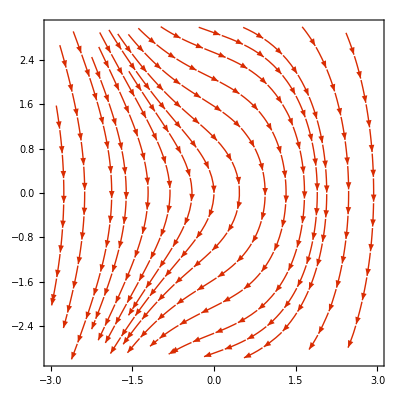
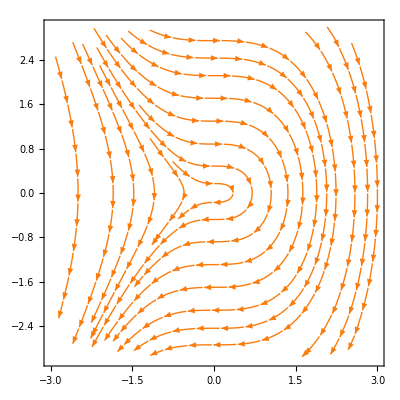
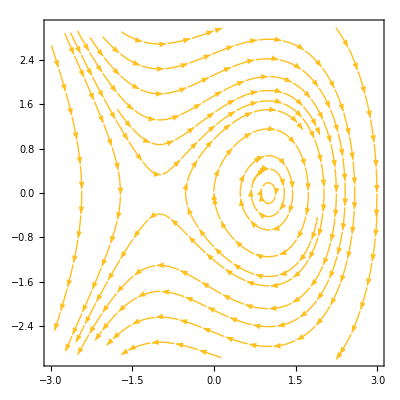

-Graphics3D-

```mathematica
stackPlots[plots2D:{__Graphics},dh_,o:OptionsPattern[Graphics3D]]:=Graphics3D[MapIndexed[Function[{g,index},g[[1]]/.Arrow[v2d_]:>Arrow[v2d/.{x_?NumericQ,y_?NumericQ}:>{x,y,dh index[[1]]}]],plots2D],o]

values={-1,0,1};plots=MapIndexed[Function[{λ,i},StreamPlot[{y,λ-x^2},{x,-3,3},{y,-3,3},StreamPoints->16,StreamScale->0.07,StreamColorFunction->None,StreamStyle->ColorData["SolarColors"][0.3i[[1]]]]],values]
plotSpacing=5;
stackPlots[plots,plotSpacing,Axes->True,Boxed->False,Ticks->{Automatic,Automatic,MapIndexed[{plotSpacing #2[[1]],Row[{"λ = ",#1}]}&,values]}]
```

```mathematica
lim=3;k0=2;st=StreamPlot3D[Ω,{kx,-k0-lim ,k0+lim},{ky,-k0-lim ,k0+lim},{kz,-lim,lim},StreamMarkers->"Arrow",StreamColorFunction->Hue,StreamColorFunctionScaling->False,StreamScale->0.1]
```

```mathematica
lim=3;k0=2;SliceVectorPlot3D[Ω,(*"CenterCutSphere"*) "CenterPlanes",{kx,-k0-lim ,k0+lim},{ky,-k0-lim ,k0+lim},{kz,-lim,lim},AxesLabel->{"k_x","k_y","k_z"}]
```

```mathematica
vp=VectorPlot3D[-Ω,{kx,-lim,lim},{ky,-lim  ,lim},{kz,-lim,lim},VectorAspectRatio->1/5,VectorPoints->7,AxesLabel->{"k_x","k_y","k_z"}];
Show[vp,cp]
```

```mathematica
(* using Function[Hue[Log[#5]/3]]*)
```

-Graphics-

### final

```mathematica
kx=0;k0=2;col=(*Function[Hue[Log[#5]/3]];*)Hue;
lim=0.5;
st=StreamDensityPlot[{Ω[[2]],Ω[[3]]},{ky,-lim-k0,lim+k0},{kz,-lim-k0  ,lim+k0},FrameLabel->{"k_y","k_z"},ColorFunction->GrayLevel,StreamColorFunction->col,StreamColorFunctionScaling->False,StreamScale->{0.015,0.015,0.015},ImageSize->350];
(*comparing with monopole flux*)
th=0.01;dr=White;
lf={Arrowheads[0.07],Arrow[{{-k0,k0/6},{-k0,-k0/6}}]};
rf={Arrowheads[0.07],Arrow[{{k0,k0/6},{k0,-k0/6}}]};
st=Show[st,Graphics[{Thickness[th],dr,lf}],Graphics[{Thickness[th],dr,rf}],LabelStyle->{Black,Bold,20,FontFamily->"Times"},Axes->False,Frame->True,FrameTicks->None,FrameLabel->{"k_y","k_z"},PlotLabel->Style[(****)"Votex nodal-ring",18,Brown]];
(****************)
lim=k0-0.05;
smp=StreamDensityPlot[{-ky/((ky^2+kz^2)^(3/2)),-kz/((ky^2+kz^2)^(3/2))},{ky,-lim,lim},{kz,-lim  ,lim},FrameLabel->{"k_y","k_z"},ColorFunction->GrayLevel,StreamColorFunction->col,StreamColorFunctionScaling->False,StreamScale->{0.015,0.015,0.015},ImageSize->350];
g0=Graphics[{PointSize[0.04],White,Point[{0,0}]}];
smp=Show[smp,g0,ImageSize->350,LabelStyle->{Black,Bold,20,FontFamily->"Times"},Axes->False,Frame->True,FrameTicks->None,FrameLabel->{"k_y","k_z"},PlotLabel->Style[(****)"Monopole",18,Brown]];
(****************)
sdp=StreamDensityPlot[{(kz ky)/((ky^2+kz^2)^(3/2)),(kz kz)/((ky^2+kz^2)^(3/2))},{ky,-lim,lim},{kz,-lim  ,lim},FrameLabel->{"k_y","k_z"},ColorFunction->GrayLevel,StreamColorFunction->col,StreamColorFunctionScaling->False,StreamScale->{0.015,0.015,0.015},ImageSize->350];
a={Arrowheads[Large],Arrow[{{0,-lim/4},{0,lim/4}}]};
g=Graphics[{Thick,White,a}];
sdp=Show[sdp,g,ImageSize->350,LabelStyle->{Black,Bold,20,FontFamily->"Times"},Axes->False,Frame->True,FrameTicks->None,FrameLabel->{"k_y","k_z"},PlotLabel->Style[(****)"Ideal dipole",18,Brown]];
gr=GraphicsRow[{smp,sdp,st},ImageSize->900]
```

```mathematica
gr=-Graphics-;SetDirectory[NotebookDirectory[]];
SetDirectory[NotebookDirectory[]];Export["bc-profile.pdf",Rasterize[gr],ImageResolution->100];
```

```mathematica
kx=0;k0=2;col=(*Function[Hue[Log[#5]/3]];*)Hue;
lim=0.5;StreamDensityPlot[{(√(kx^2+ky^2)-k0)^2,kz},{ky,-lim,lim},{kz,-lim  ,lim},FrameLabel->{"k_y","k_z"},ColorFunction->GrayLevel,StreamColorFunction->col,StreamColorFunctionScaling->False,StreamScale->{0.015,0.015,0.015},ImageSize->350]
Clear[kx];
```

```mathematica
kz=1;k0=2;col=(*Function[Hue[Log[#5]/3]];*)Hue;
lim=0.5;StreamDensityPlot[{(√(kx^2+ky^2)-k0)^2,kz},{kx,-lim,lim},{ky,-lim  ,lim},FrameLabel->{"k_y","k_z"},ColorFunction->GrayLevel,StreamColorFunction->col,StreamColorFunctionScaling->False,StreamScale->{0.015,0.015,0.015},ImageSize->350]
Clear[kx,kz];
```